# A Mathematical Exploration through Mathematica with a problem from Rudin’s Principles of Mathematical Analysis

This essay illustrates an example of how a mathematics student might go about exploring and extending a problem through Mathematica.

Nikki Sigurdson, Jun. 24, 2018

Problem 19 in chapter 1 of Walter Rudin's Principles of Mathematical Analysis, 3rd ed. asks students to consider a specific concept- and this premise offers students a starting point for exploring a related, broader question. By exploring extensions of their problems, students can develop their mathematical intuition, and Mathematica offers them a powerful, quick way to do so.

## Problem Outline

Problem 19 is as follows:

Suppose  a, b  ∈  ℝ^k. Find  c  ∈  ℝ^k and r  > 0 such that   |x - a | = 2 |x - b| if and only if |x - c| = r.

Here’s a related question: what is the set of all x ∈  ℝ^k such that |x - a | = 2 |x - b|  holds? We can explore this problem through Mathematica. Pen-and-paper explorations suggested to me that there existed many possible solutions in the  ℝ^2 case. In the visualizations below, those solutions are depicted by large red points. Below is an example of this idea:

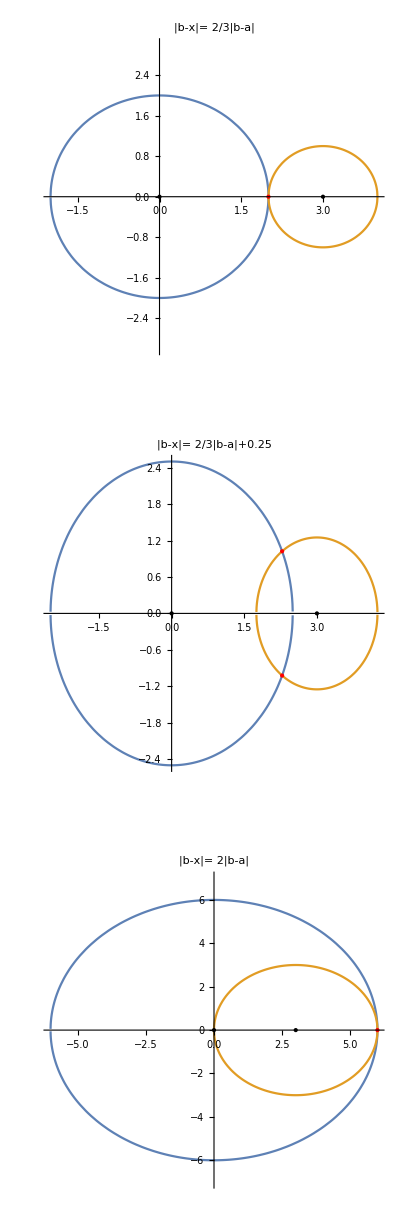

```mathematica
Clear[x];
a = {0,0};
b = {3,0};

c = (b[[1]]-a[[1]])/3;
g = Graphics[{PointSize[Large], Black, Point[a]}];
h = Graphics[{PointSize[Large], Black, Point[b]}];

circlesols= NSolve[x^2 + y^2 == (2 (c+0.25))^2 && (x-b[[1]])^2 + y^2 == (c+0.25)^2, {x, y}, Reals];
sols = {x,y} /. circlesols;

p2a = Graphics[{PointSize[Large], Red, Point[sols[[1]]]}];
p2b = Graphics[{PointSize[Large], Red, Point[sols[[2]]]}];

p1 =  Graphics[{PointSize[Large], Red, Point[ {2/3  b[[1]]-a[[1]], 0 }]}] ;
p3 = Graphics[{PointSize[Large], Red, Point[ {2 b[[1]]-a[[1]], 0 }]}] ;

m = Plot[ { 	
	y/.Solve[x^2+y^2== (2 (c))^2], 
	y/. Solve[(x-b[[1]])^2+y^2 == (c)^2 ]   },  {x,-10, 10}, AspectRatio->Automatic , PlotRange->{-3,3}, PlotLabel->"|b-x|= 2/3|b-a|" ];

p = Plot[ { 
	y/.Solve[x^2+y^2== (2 (c+0.25))^2], 
	y/. Solve[(x-b[[1]])^2+y^2 == (c+0.25)^2 ]  }, {x,-10, 10}, AspectRatio->Automatic , PlotRange->{-2.5,2.5}, PlotLabel->"|b-x|= 2/3|b-a|+0.25" ];
	
n = Plot[ { 
	y/.Solve[x^2+y^2== (2 (3))^2], 
	y/. Solve[(x-b[[1]])^2+y^2 == (3)^2 ]  }, {x,-10, 10}, AspectRatio->Automatic ,PlotRange->{-7,7}, PlotLabel->"|b-x|= 2|b-a|"];

GraphicsGrid[ { {Show[m,g,h, p1]}, {Show[p,g,h, p2a,p2b]}, {Show[n,g,h, p3]}}]
```

In the next section, we will further explore the geometry and structure of the set of all solutions in the two dimensional real plane.

## Discovering All the Solutions

First, let’s pick some concrete and arbitrary a and b to work with.  Let’s also give the abstract notion of  |x - b| some variable name too. Let  |x - b| = alpha and let’s initialize it to some starting value.

```mathematica
a = {0,0};
b = {3,0};
alpha = 2;
```

We want to be able to  visualize a plot with circles, and be able to dynamically manipulate the variable alpha so that we can change the size of the circles. Below is a snippet of code which allows us to begin exploring what the solution set could be. Remember that our solutions x will be all the intersections of the circles, for all values of alpha. One can play around with the values of alpha below through the scale to develop an intuition about why the shape of the set of solutions x will look like circle too.

```mathematica
g = Graphics[{PointSize[Large], Black, Point[a]}];
h = Graphics[{PointSize[Large], Black, Point[b]}];

Manipulate[  Show[ Plot[ {y/.Solve[x^2+y^2== (2 alpha)^2], y /. Solve[(x-b[[1]])^2+y^2==(alpha)^2]},  
	{x,-7,9}, AspectRatio->Automatic, PlotRange->All], g,h ],
{alpha,0.5 ,3.5, 0.5}
]
```

Now that we’ve seen  what we are working with, let's try to collect all those intersection points into a list.

This next bit of code allows us get the intersection points for any one specific alpha.

```mathematica
NSolve[x^2 + y^2 == Sqrt[2 alpha] && (x-b[[1]])^2 + y^2 == Sqrt[alpha] ,{x, y}, Reals];
```

But we want the intersection points for lots of alphas. To do this we are going to re-write the line above into a lambda function, and then use /@ to input a list of alpha values and have our function circlesols evaluate for each list-item individually.

```mathematica
circlesols = NSolve[x^2 + y^2 == Sqrt[2 #] && (x - b[[1]])^2 + y^2 == Sqrt[#] , {x, y}, Reals] &; 
sols = circlesols /@ Range[0, 10, 0.1];
```

Our next problem is that the code above produces a set possessing the right information, but in the wrong format. The next bit of code will fix that and present the data in a form which we can easily continue to work with (which is a list of lists of the form {a,b} ) .

```mathematica
circlesols = NSolve[x^2 + y^2 == Sqrt[2 #] && (x - b[[1]])^2 + y^2 == Sqrt[#] , {x, y}, Reals] &; 
sols = {x,y} /. Flatten[circlesols /@ Range[0,30,0.1], 1];
```

Now, let’s try plotting these new-found solutions.

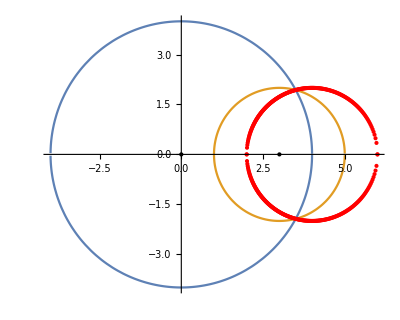

```mathematica
g = Graphics[{PointSize[Large], Black, Point[a]}];
h = Graphics[{PointSize[Large], Black, Point[b]}];

circlesols= NSolve[x^2 + y^2 == (2 #)^2 && (x-b[[1]])^2 + y^2 == (#)^2,{x, y}, Reals] & ; 
sols = {x,y} /. Flatten[circlesols /@ Range[0,20,0.01], 1];
solutions = ListPlot[sols, PlotStyle->Red,  PlotRegion-> {{-5,8 } ,{-5,22}}];

m= Plot[ { 	
	y/.Solve[x^2+y^2== (2 (c))^2], 
	y/. Solve[(x-b[[1]])^2+y^2 == (c)^2 ]   },  {x,-5, 100},
 AspectRatio->Automatic, PlotRange->{-4,4}    ];

Show[ Plot[ {y/.Solve[x^2+y^2== (2 alpha)^2], y /. Solve[(x-b[[1]])^2+y^2==(alpha)^2]},  
	{x,-7,9}, AspectRatio->Automatic, PlotRange->All], ListPlot[sols, PlotStyle->Red,  PlotRegion-> {{-5,8 } ,{-5,22}}], g, h ]
```

Since we are working computationally, our solutions appear as discrete points in the graph above-- but it’s clear the solutions really fall on a continuous curve.

The next piece of code plots our solutions over a dynamic graph and illustrates how each solution point is found as the intersection of our two circles.

```mathematica
g = Graphics[{PointSize[Large], Black, Point[a]}];
h = Graphics[{PointSize[Large], Black, Point[b]}];

circlesols= NSolve[x^2 + y^2 == (2 #)^2 && (x-b[[1]])^2 + y^2 == (#)^2,{x, y}, Reals] & ; 
sols = {x,y} /. Flatten[circlesols /@ Range[0,20,0.1], 1];
solutions = ListPlot[sols, PlotStyle->Red,  PlotRegion-> {{-5,8 } ,{-5,10}}];

Manipulate[  Show[ Plot[ {y/.Solve[x^2+y^2== (2 alpha)^2], y /. Solve[(x-b[[1]])^2+y^2==(alpha)^2]},  
	{x,-7,9}, AspectRatio->Automatic, PlotRange->All], ListPlot[sols, PlotStyle->Red,  PlotRegion-> {{-5,8 } ,{-5,22}}], g,h ],
{alpha,0.5 ,3.5, 0.5}
]
```

And there we go!

## Afterward

As a future additional extension, it might also be nice to be able to see the solutions dynamically appear on that last graph as the user adjusts the value of alpha.

Many problems in mathematics-even proof-based ones- can be explored through Mathematica. I would like to challenge other students to utilize Mathematica and similar tools to develop their mathematical intuition and understanding as well.

## Author contact information

n.sigurdson [at] mail.utoronto.ca

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

### Code